```mathematica
δ1 = {1,0};
δ2 = {0.5,-0.5};
δ3= {-0.5,-0.5};
```

{{0.,0.},{1.,0.},{2.,0.},{-0.5,-0.5},{0.5,-0.5},{1.5,-0.5},{2.5,-0.5},{-1.,-1.},{0.,-1.},{1.,-1.},{2.,-1.},{3.,-1.},{-0.5,-1.5},{0.5,-1.5},{1.5,-1.5},{2.5,-1.5},{0.,-2.},{1.,-2.},{2.,-2.}}

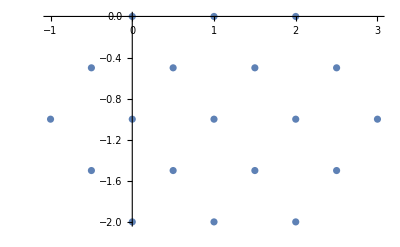

```mathematica
L=3;
data = Partition[Flatten[
Table[nx*δ1+If[ny<L,ny*δ3,(L-1)*δ3+(ny-L+1)*δ2],{ny,0,2L-2},{nx,0,L-1+If[ny<L,ny,2L-2-ny]}]
],2]
ListPlot[data,PlotRange->Full]
```

```mathematica
SetDirectory[NotebookDirectory[]]
chirality = Import["chiralproduct.csv"];
tuplesInvolved = Import["chiralproduct_tuples.csv"];
```

/Users/andreashaller/exact_diagonalization

{{1.,1.,-0.0399483},{2.,1.,-0.0418411},{3.,1.,-0.0433261},{4.,1.,-0.0444904},{5.,1.,-0.0481366},{6.,1.,-0.0419205},{7.,1.,-0.0420201},{8.,1.,-0.0421134},{9.,1.,-0.0422006},{10.,1.,-0.042282},{11.,1.,-0.0423577},{12.,1.,-0.0424281},{13.,1.,-0.0424931},{14.,1.,-0.0425531},{15.,1.,-0.0426082},{16.,1.,-0.0426586},{17.,1.,-0.0427044},{18.,1.,-0.0427458},{19.,1.,-0.0427829},{20.,1.,-0.042816},{21.,1.,-0.042845},{22.,1.,-0.0428702},{23.,1.,-0.0428916},{24.,1.,-0.0429095},{1.,1.,-0.0429239},{2.,1.,-0.0429349},{3.,1.,-0.0429426},{4.,1.,-0.0429472},{5.,1.,-0.0429487},{6.,1.,-0.0429473},{7.,1.,-0.042943},{8.,1.,-0.0429359},{9.,1.,-0.0429262},{10.,1.,-0.0429139},{11.,1.,-0.042899},{12.,1.,-0.0428818},{13.,1.,-0.0428621},{14.,1.,-0.0428402},{15.,1.,-0.0428161},{16.,1.,-0.0427899},{17.,1.,-0.0427615},{18.,1.,-0.0427312},{19.,1.,-0.0439784},{20.,1.,-0.0435871},{21.,1.,-0.0431809},{22.,1.,-0.0427599},{23.,1.,-2.25485×10^-25},{24.,1.,-3.903×10^-28}}

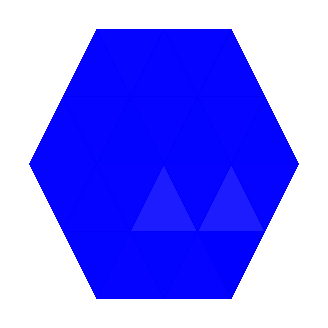

```mathematica
selection=Select[chirality[[6*24+1;;6*24+4 24-3]],#[[2]]==1&];
selection
selection[[All,3]]=selection[[All,3]]/Max[Abs[selection[[All,3]]]];
Graphics[Table[{Directive[If[sel[[3]]<0,Blue,Red],Opacity[Abs[sel[[3]]]]],Triangle[data[[tuplesInvolved[[sel[[1]]]]]]]},{sel,selection}],AspectRatio->1]
```